## Thermal effects on a Global monopole spacetime

## with Robin boundary conditions

ds^2= -dt^2+dr^2+α^2 r^2 dθ^2 + α^2 r^2 Sin[θ]^2 dϕ^2

This notebook contains the implmentations of the the transition rate, the thermal fluctuations and the energy density, as defined in the paper ["Thermal effects on a global monopole with Robin boundary conditions"](https://arxiv.org/abs/2108.12236). The plots here are simplified versions merely for illustration, but with the implementations of this notebook it is straightforward to reproduce our results. For more information regarding the numerical analysis, one can contact me at lissa.desouzacampos01@universitadipavia.it.

I import four of my personal packages: ["CurvatureTensors"](https://github.com/lissadesouzacampos/CurvatureTensors), ["ScalarWaveEquation"](https://github.com/lissadesouzacampos/ScalarWaveEquation),  ["ODEsTransformations"](https://github.com/lissadesouzacampos/ODEsTransformations), and ["LatexPlot"](https://github.com/lissadesouzacampos/latex_style) for the following;
and I also import ["MaTeX"](https://github.com/szhorvat/MaTeX) and ["CustomTicks"](https://github.com/mark-caprio/CustomTicks).

## Geometry

```mathematica
Import["C:\\Users\\Lissa\\Google Drive\\Mathematica\\MyPackages\\CurvatureTensors.m"]
```

```mathematica
metric=DiagonalMatrix[{-1,1,α^2 r^2,α^2 r^2 Sin[θ]^2}];
coordinates={t,r,θ,ϕ};
CurvatureTensors[metric,coordinates]
```

```mathematica
RicciScalar
```

(2-2 α^2)/(r^2 α^2)

```mathematica
KretschmannScalar
```

(4 (-1+α^2)^2)/(r^4 α^4)

```mathematica
PrettyEinstein[]
```

G_(RowBox[{) = (1-α^2)/(r^2 α^2)
G_(RowBox[{) = (-1+α^2)/(r^2 α^2)

```mathematica
PrettyRiemann[]
```

(R_(RowBox[{))^(RowBox[{) = 1-α^2
(R_(RowBox[{))^(RowBox[{) = (-1+α^2) Sin[θ]^2
(R_(RowBox[{))^(RowBox[{) = -1+α^2
(R_(RowBox[{))^(RowBox[{) = -(-1+α^2) Sin[θ]^2

```mathematica
PrettyRicci[]
```

R_(RowBox[{) = 1-α^2
R_(RowBox[{) = -(-1+α^2) Sin[θ]^2

## Klein-Gordon equation

```mathematica
Quiet[Import["C:\\Users\\Lissa\\Google Drive\\Mathematica\\MyPackages\\ScalarWaveEquation.m"];Import["C:\\Users\\Lissa\\Google Drive\\Mathematica\\MyPackages\\ODEsTransformations.m"]]
```

```mathematica
ScalarWaveEquation["diagonal_metric"->{-1,1,α^2 r^2,α^2 r^2 Sin[θ]^2} , "ansatz"->{ ⅇ^(-ⅈ ω t),R[r], Y[θ,φ]},"mass"->m,"coordinates"->{t,r,θ,ϕ}]
```

-m^2+ω^2+(2 R'[r]+r R''[r])/(r R[r])+(Cot[θ] Y^(1,0)[θ,φ]+Y^(2,0)[θ,φ])/(r^2 α^2 Y[θ,φ])

Let m^2 = m_0^2 +ξ R:

```mathematica
Clear[λ];radialEq= r^2(R''[r] + 2/r  R'[r]+(k^2-λ/r^2)R[r]);
DSolve[radialEq==0,R[r],r]
```

{{R[r]→C[1] SphericalBesselJ[1/2 (-1+√(1+4 λ)),k r]+C[2] SphericalBesselY[1/2 (-1+√(1+4 λ)),k r]}}

where the auxiliary parameter λ is defined as:

λ=(l(l+1)+2ξ (1-α^2))/α^2;(*always positive*)

Let us also define the auxiliary parameter ν, the index of the spherical Bessel functions:

ν=1/2 (-1+√(1+4 λ));

In Minkowski, it simplifies to:

```mathematica
radialEqMink= r^2(R''[r] + 2/r  R'[r]+(k^2-((l(l+1)+2ξ(1-α^2))/α^2)/r^2)R[r])/.α->1;
DSolve[radialEqMink==0,R[r],r]
```

{{R[r]→C[1] SphericalBesselJ[l,k r]+C[2] SphericalBesselY[l,k r]}}

### In Sturm-Liouville form

```mathematica
Clear[λ,ν];SturmLiouvilleForm[radialEq,R,r,k^2]
```

{k^2 R[r]==-1/r^2 (d/(d r) (r^2 d/(d r))-λ) R[r],r^2,-λ,-r^2}

```mathematica
measure[r_]=r^2;
```

### Basis

```mathematica
R10[r_]:=SphericalBesselJ[ν,k  r];
R20[r_]:=k SphericalBesselY[ν,k  r];
```

```mathematica
measure[r]Wronskian[{R10[r],R20[r]},r]
```

1

## Minimal coupling

### Transition rate

#### Definitions

```mathematica
ξ=0;
ν=1/2 (-1+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2));
ν0=1/2 (-1+√((α^2+8 ξ-8 α^2 ξ)/α^2));
Transition[α0_,β_,γ_,Ω0_,r_,lmax_]:=1/α^2 1/(2π)Sign[Ω]/(ⅇ^(Sign[Ω] β  ω)-1)(    k/(Cos[γ]^2+k^2 Sin[γ]^2)( Cos[γ]SphericalBesselJ[ν0,k r] - Sin[γ]k  SphericalBesselY[ν0,k r])^2+k Sum[(2l+1)SphericalBesselJ[ ν,k r]^2,{l,1,lmax}])/.k->ω/.ω-> Abs[Ω]/.α->α0/.Ω->Ω0;
```

#### Dirichlet

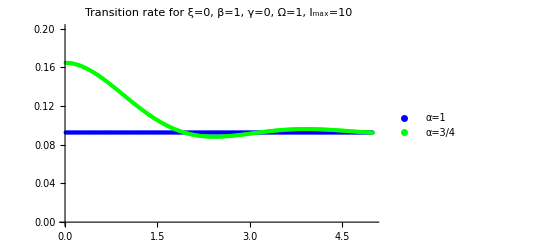

```mathematica
βp=1;
γp=0;
Ωp=1;
lmax=10;
p1=ListPlot[Table[{r,Transition[1,βp,γp,Ωp,r,lmax]},{r,Range[1/100,5,1/50]}],PlotStyle->{Thick,Blue},PlotLegends->{"α=1"},PlotRange->All];
p2=ListPlot[Table[{r,Transition[3/4,βp,γp,Ωp,r,lmax]},{r,Range[1/100,5,1/50]}],PlotStyle->{Thick,Green},PlotLegends->{"α=3/4"},PlotRange->All];
Show[p1,p2,PlotRange->{0,0.2},PlotLabel-> "Transition rate for ξ=0, β=1, γ=0, Ω=1, l_max=10"]
```

#### Robin

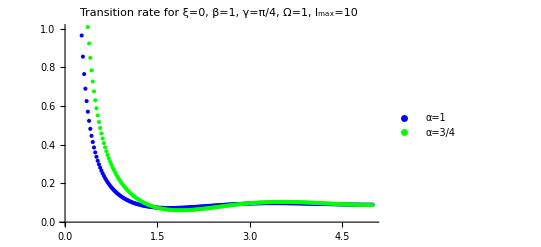

```mathematica
βp=1;
γp=π/4;
Ωp=1;
lmax=10;
p1=ListPlot[Table[{r,Transition[1,βp,γp,Ωp,r,lmax]},{r,Range[1/100,5,1/50]}],PlotStyle->{Thick,Blue},PlotLegends->{"α=1"},PlotRange->All];
p2=ListPlot[Table[{r,Transition[3/4,βp,γp,Ωp,r,lmax]},{r,Range[1/100,5,1/50]}],PlotStyle->{Thick,Green},PlotLegends->{"α=3/4"},PlotRange->All];
Show[p1,p2,PlotRange->{0,1},PlotLabel-> "Transition rate for ξ=0, β=1, γ=π/4, Ω=1, l_max=10"]
```

### Thermal fluctuations

#### Definitions

```mathematica
ξ=0;
cΔG =((1+2 l) ω (Cos[γ] SphericalBesselJ[1/2 (-1+√(1+(4 l (1+l))/α^2)),r ω]-ω Sin[γ] SphericalBesselY[1/2 (-1+√(1+(4 l (1+l))/α^2)),r ω])^2)/(2 (-1+ⅇ^(β ω)) π^2 α^2 (Cos[γ]^2+ω^2 Sin[γ]^2));
summandΔG[α0_?NumericQ,β0_?NumericQ,γ0_?NumericQ, r0_?NumericQ,l0_?NumericQ]:=NIntegrate[cΔG /.{α->α0,β->β0,γ->If[l0==0,γ0,0],r->r0,l->l0},{ω,0,∞},AccuracyGoal->5,WorkingPrecision->20]

ΔG[α0_?NumericQ,β0_?NumericQ,γ0_?NumericQ,r0_?NumericQ,lmax_?NumericQ]:= Sum[summandΔG[α0,β0,γ0,r0,l],{l,0,lmax}]
```

#### Dirichlet

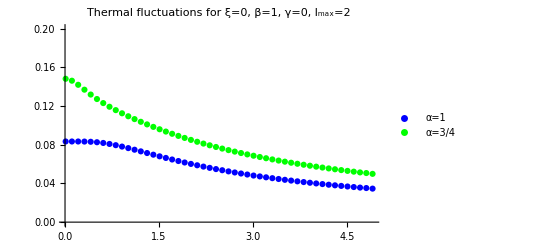

```mathematica
βp=1;
γp=0;
lmax=2;
p1=ListPlot[Table[{r,ΔG[1,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Blue},PlotLegends->{"α=1"},PlotRange->All];
p2=ListPlot[Table[{r,ΔG[3/4,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Green},PlotLegends->{"α=3/4"},PlotRange->All];
Show[p1,p2,PlotRange->{0,0.2},PlotLabel-> "Thermal fluctuations for ξ=0, β=1, γ=0, l_max=2"]
```

#### Robin

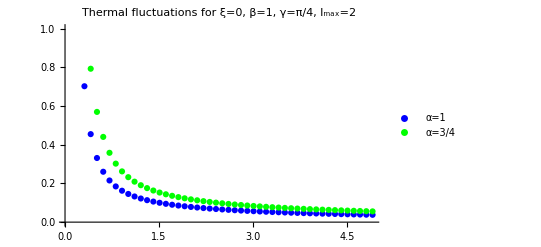

```mathematica
βp=1;
γp=π/4;
lmax=2;
p1=ListPlot[Table[{r,ΔG[1,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Blue},PlotLegends->{"α=1"},PlotRange->All];
p2=ListPlot[Table[{r,ΔG[3/4,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Green},PlotLegends->{"α=3/4"},PlotRange->All];
Show[p1,p2,PlotRange->{0,1},PlotLabel-> "Thermal fluctuations for ξ=0, β=1, γ=π/4, l_max=2"]
```

### Energy density

#### Definitions

```mathematica
cDΔG=-(((1+2 l) ω (-4 l (1+l) (Cos[γ] SphericalBesselJ[1/2 (-1+√(1+(4 l (1+l))/α^2)),r ω]-ω Sin[γ] SphericalBesselY[1/2 (-1+√(1+(4 l (1+l))/α^2)),r ω])^2+4 r^2 α^2 ω^2 (Cos[γ] SphericalBesselJ[1/2 (-1+√(1+(4 l (1+l))/α^2)),r ω]-ω Sin[γ] SphericalBesselY[1/2 (-1+√(1+(4 l (1+l))/α^2)),r ω])^2-α^2 (-r ω Cos[γ] SphericalBesselJ[1/2 (-3+√(1+(4 l (1+l))/α^2)),r ω]+Cos[γ] SphericalBesselJ[1/2 (-1+√(1+(4 l (1+l))/α^2)),r ω]+r ω Cos[γ] SphericalBesselJ[1/2 (1+√(1+(4 l (1+l))/α^2)),r ω]+ω Sin[γ] (r ω SphericalBesselY[1/2 (-3+√(1+(4 l (1+l))/α^2)),r ω]-SphericalBesselY[1/2 (-1+√(1+(4 l (1+l))/α^2)),r ω]-r ω SphericalBesselY[1/2 (1+√(1+(4 l (1+l))/α^2)),r ω]))^2-8 r^2 α^2 ω^2 (Cos[γ] SphericalBesselJ[1/2 (-1+√((4 l+4 l^2+α^2)/α^2)),r ω]-ω Sin[γ] SphericalBesselY[1/2 (-1+√((4 l+4 l^2+α^2)/α^2)),r ω])^2))/(16 (-1+ⅇ^(β ω)) π^2 r^2 α^4 (Cos[γ]^2+ω^2 Sin[γ]^2)));
summandTtt[α0_?NumericQ,β0_?NumericQ,γ0_?NumericQ,r0_?NumericQ,l0_?NumericQ]:=NIntegrate[cDΔG/.{ α->α0,β->β0,γ->If[l0==0,γ0,0],r->r0,l->l0},{ω,0,∞},PrecisionGoal->5]

Ttt[α0_?NumericQ,β0_?NumericQ,γ0_?NumericQ,r0_?NumericQ,lmax_?NumericQ]:= Sum[summandTtt[α0,β0,γ0,r0,l],{l,0,lmax}]
```

#### Dirichlet

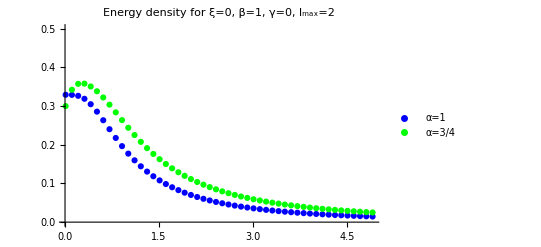

```mathematica
βp=1;
γp=0;
lmax=2;
p1=ListPlot[Table[{r,Ttt[1,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Blue},PlotLegends->{"α=1"},PlotRange->All];
p2=ListPlot[Table[{r,Ttt[3/4,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Green},PlotLegends->{"α=3/4"},PlotRange->All];
Show[p1,p2,PlotRange->{0,1/2},PlotLabel-> "Energy density for ξ=0, β=1, γ=0, l_max=2"]
```

#### Robin

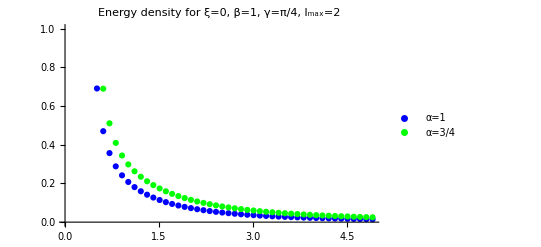

```mathematica
βp=1;
γp=π/4;
lmax=2;
p1=ListPlot[Table[{r,Ttt[1,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Blue},PlotLegends->{"α=1"},PlotRange->All];
p2=ListPlot[Table[{r,Ttt[3/4,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Green},PlotLegends->{"α=3/4"},PlotRange->All];
Show[p1,p2,PlotRange->{0,1},PlotLabel-> "Energy density for ξ=0, β=1, γ=π/4, l_max=2"]
```

## Conformal coupling

### Transition rate

#### Definitions

```mathematica
ξ=1/6;
ν=1/2 (-1+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2));
ν0=1/2 (-1+√((α^2+8 ξ-8 α^2 ξ)/α^2));
Transition[α0_,β_,γ_,Ω0_,r_,lmax_]:=1/α^2 1/(2π)Sign[Ω]/(ⅇ^(Sign[Ω] β  ω)-1)(    k/(Cos[γ]^2+k^2 Sin[γ]^2)( Cos[γ]SphericalBesselJ[ν0,k r] - Sin[γ]k  SphericalBesselY[ν0,k r])^2+k Sum[(2l+1)SphericalBesselJ[ ν,k r]^2,{l,1,lmax}])/.k->ω/.ω-> Abs[Ω]/.α->α0/.Ω->Ω0;
```

#### Dirichlet

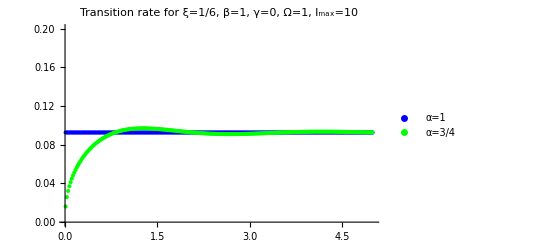

```mathematica
βp=1;
γp=0;
Ωp=1;
lmax=10;
p1=ListPlot[Table[{r,Transition[1,βp,γp,Ωp,r,lmax]},{r,Range[1/100,5,1/50]}],PlotStyle->{Thick,Blue},PlotLegends->{"α=1"},PlotRange->All];
p2=ListPlot[Table[{r,Transition[3/4,βp,γp,Ωp,r,lmax]},{r,Range[1/100,5,1/50]}],PlotStyle->{Thick,Green},PlotLegends->{"α=3/4"},PlotRange->All];
Show[p1,p2,PlotRange->{0,0.2},PlotLabel-> "Transition rate for ξ=1/6, β=1, γ=0, Ω=1, l_max=10"]
```

#### Robin

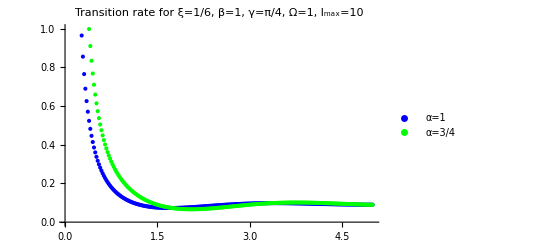

```mathematica
βp=1;
γp=π/4;
Ωp=1;
lmax=10;
p1=ListPlot[Table[{r,Transition[1,βp,γp,Ωp,r,lmax]},{r,Range[1/100,5,1/50]}],PlotStyle->{Thick,Blue},PlotLegends->{"α=1"},PlotRange->All];
p2=ListPlot[Table[{r,Transition[3/4,βp,γp,Ωp,r,lmax]},{r,Range[1/100,5,1/50]}],PlotStyle->{Thick,Green},PlotLegends->{"α=3/4"},PlotRange->All];
Show[p1,p2,PlotRange->{0,1},PlotLabel-> "Transition rate for ξ=1/6, β=1, γ=π/4, Ω=1, l_max=10"]
```

### Thermal fluctuations

#### Definitions

```mathematica
ξ=1/6;
cΔG =((1+2 l) ω (Cos[γ] SphericalBesselJ[1/6 (-3+√((12+36 l+36 l^2-3 α^2)/α^2)),r ω]-ω Sin[γ] SphericalBesselY[1/6 (-3+√((12+36 l+36 l^2-3 α^2)/α^2)),r ω])^2)/(2 (-1+ⅇ^(β ω)) π^2 α^2 (Cos[γ]^2+ω^2 Sin[γ]^2));
summandΔG[α0_?NumericQ,β0_?NumericQ,γ0_?NumericQ, r0_?NumericQ,l0_?NumericQ]:=NIntegrate[cΔG /.{α->α0,β->β0,γ->If[l0==0,γ0,0],r->r0,l->l0},{ω,0,∞},AccuracyGoal->5,WorkingPrecision->40]
ΔG[α0_?NumericQ,β0_?NumericQ,γ0_?NumericQ,r0_?NumericQ,lmax_?NumericQ]:= Sum[summandΔG[α0,β0,γ0,r0,l],{l,0,lmax}]
```

#### Dirichlet

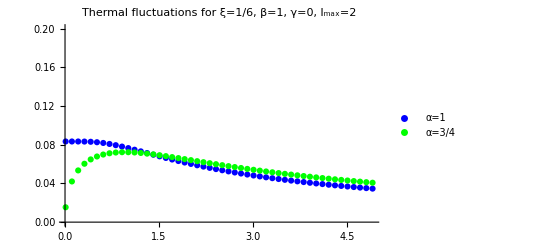

```mathematica
βp=1;
γp=0;
lmax=2;
p1=ListPlot[Table[{r,ΔG[1,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Blue},PlotLegends->{"α=1"},PlotRange->All];
p2=ListPlot[Table[{r,ΔG[3/4,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Green},PlotLegends->{"α=3/4"},PlotRange->All];
Show[p1,p2,PlotRange->{0,0.2},PlotLabel-> "Thermal fluctuations for ξ=1/6, β=1, γ=0, l_max=2"]
```

#### Robin

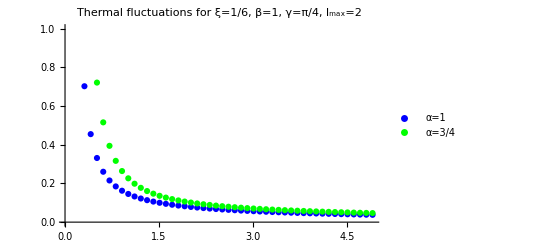

```mathematica
βp=1;
γp=π/4;
lmax=2;
p1=ListPlot[Table[{r,ΔG[1,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Blue},PlotLegends->{"α=1"},PlotRange->All];
p2=ListPlot[Table[{r,ΔG[3/4,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Green},PlotLegends->{"α=3/4"},PlotRange->All];
Show[p1,p2,PlotRange->{0,1},PlotLabel-> "Thermal fluctuations for ξ=1/6, β=1, γ=π/4, l_max=2"]
```

### Energy density

#### Definitions

```mathematica
ξ=1/6;
cDΔG=-(((1+2 l) ω (4 (-1+α^2) ξ (Cos[γ] SphericalBesselJ[1/2 (-1+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]-ω Sin[γ] SphericalBesselY[1/2 (-1+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω])^2-8 r^2 α^2 ξ ω^2 (Cos[γ] SphericalBesselJ[1/2 (-1+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]-ω Sin[γ] SphericalBesselY[1/2 (-1+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω])^2+4 r^2 α^2 (-1+2 ξ) ω^2 (Cos[γ] SphericalBesselJ[1/2 (-1+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]-ω Sin[γ] SphericalBesselY[1/2 (-1+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω])^2+2 ξ (-r^2 α^2 ω^2 Cos[γ] SphericalBesselJ[1/2 (-5+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]-2 r α^2 ω Cos[γ] SphericalBesselJ[1/2 (-3+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]+2 r α^2 ω Cos[γ] SphericalBesselJ[1/2 (1+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]-r^2 α^2 ω^2 Cos[γ] SphericalBesselJ[1/2 (3+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]+4 l Cos[γ] SphericalBesselJ[1/2 (-1+√(1+(4 (l+l^2+2 ξ-2 α^2 ξ))/α^2)),r ω]+4 l^2 Cos[γ] SphericalBesselJ[1/2 (-1+√(1+(4 (l+l^2+2 ξ-2 α^2 ξ))/α^2)),r ω]+α^2 Cos[γ] SphericalBesselJ[1/2 (-1+√(1+(4 (l+l^2+2 ξ-2 α^2 ξ))/α^2)),r ω]-2 r^2 α^2 ω^2 Cos[γ] SphericalBesselJ[1/2 (-1+√(1+(4 (l+l^2+2 ξ-2 α^2 ξ))/α^2)),r ω]+r^2 α^2 ω^3 Sin[γ] SphericalBesselY[1/2 (-5+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]+2 r α^2 ω^2 Sin[γ] SphericalBesselY[1/2 (-3+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]-2 r α^2 ω^2 Sin[γ] SphericalBesselY[1/2 (1+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]+r^2 α^2 ω^3 Sin[γ] SphericalBesselY[1/2 (3+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]-4 l ω Sin[γ] SphericalBesselY[1/2 (-1+√(1+(4 (l+l^2+2 ξ-2 α^2 ξ))/α^2)),r ω]-4 l^2 ω Sin[γ] SphericalBesselY[1/2 (-1+√(1+(4 (l+l^2+2 ξ-2 α^2 ξ))/α^2)),r ω]-α^2 ω Sin[γ] SphericalBesselY[1/2 (-1+√(1+(4 (l+l^2+2 ξ-2 α^2 ξ))/α^2)),r ω]+2 r^2 α^2 ω^3 Sin[γ] SphericalBesselY[1/2 (-1+√(1+(4 (l+l^2+2 ξ-2 α^2 ξ))/α^2)),r ω]) (-Cos[γ] SphericalBesselJ[1/2 (-1+√(1+(4 (l+l^2-2 (-1+α^2) ξ))/α^2)),r ω]+ω Sin[γ] SphericalBesselY[1/2 (-1+√(1+(4 (l+l^2-2 (-1+α^2) ξ))/α^2)),r ω])+(1/2-2 ξ) (-α^2 (r ω Cos[γ] SphericalBesselJ[1/2 (-3+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]-r ω Cos[γ] SphericalBesselJ[1/2 (1+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]-Cos[γ] SphericalBesselJ[1/2 (-1+√(1+(4 (l+l^2+2 ξ-2 α^2 ξ))/α^2)),r ω]-r ω^2 Sin[γ] SphericalBesselY[1/2 (-3+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]+r ω^2 Sin[γ] SphericalBesselY[1/2 (1+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2)),r ω]+ω Sin[γ] SphericalBesselY[1/2 (-1+√(1+(4 (l+l^2+2 ξ-2 α^2 ξ))/α^2)),r ω])^2-4 l (1+l) (Cos[γ] SphericalBesselJ[1/2 (-1+√(1+(4 (l+l^2-2 (-1+α^2) ξ))/α^2)),r ω]-ω Sin[γ] SphericalBesselY[1/2 (-1+√(1+(4 (l+l^2-2 (-1+α^2) ξ))/α^2)),r ω])^2+4 r^2 α^2 ω^2 (Cos[γ] SphericalBesselJ[1/2 (-1+√(1+(4 (l+l^2-2 (-1+α^2) ξ))/α^2)),r ω]-ω Sin[γ] SphericalBesselY[1/2 (-1+√(1+(4 (l+l^2-2 (-1+α^2) ξ))/α^2)),r ω])^2)))/(8 (-1+ⅇ^(β ω)) π^2 r^2 α^4 (Cos[γ]^2+ω^2 Sin[γ]^2)));
summandTtt[α0_?NumericQ,β0_?NumericQ,γ0_?NumericQ,r0_?NumericQ,l0_?NumericQ]:=NIntegrate[cDΔG/.{ α->α0,β->β0,γ->If[l0==0,γ0,0],r->r0,l->l0},{ω,0,∞},PrecisionGoal->5]

Ttt[α0_?NumericQ,β0_?NumericQ,γ0_?NumericQ,r0_?NumericQ,lmax_?NumericQ]:= Sum[summandTtt[α0,β0,γ0,r0,l],{l,0,lmax}]
```

#### Dirichlet

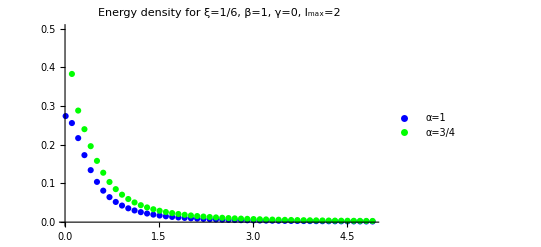

```mathematica
βp=1;
γp=0;
lmax=0;
p1=ListPlot[Table[{r,Ttt[1,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Blue},PlotLegends->{"α=1"},PlotRange->All];
p2=ListPlot[Table[{r,Ttt[3/4,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Green},PlotLegends->{"α=3/4"},PlotRange->All];
Show[p1,p2,PlotRange->{0,1/2},PlotLabel-> "Energy density for ξ=1/6, β=1, γ=0, l_max=2"]
```

#### Robin

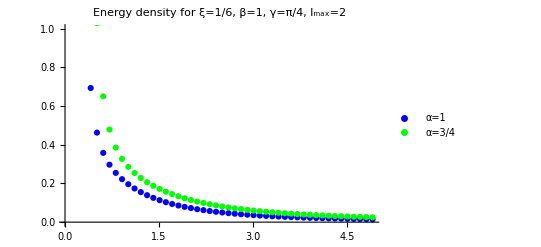

```mathematica
βp=1;
γp=π/4;
lmax=2;
p1=ListPlot[Table[{r,Ttt[1,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Blue},PlotLegends->{"α=1"},PlotRange->All];
p2=ListPlot[Table[{r,Ttt[3/4,βp,γp,r,lmax]},{r,Range[1/100,5,1/10]}],PlotStyle->{Thick,Green},PlotLegends->{"α=3/4"},PlotRange->All];
Show[p1,p2,PlotRange->{0,1},PlotLabel-> "Energy density for ξ=1/6, β=1, γ=π/4, l_max=2"]
```

## Example of formatting a plot

Just to illustrate how to take a standard Mathematica plot and format it as in the paper.

#### Definitions for Plots

```mathematica
Needs["MaTeX`"]
Get["C:\\Users\\Lissa\\Google Drive\\Mathematica\\OthersPackages\\CustomTicks-2.1.0\\CustomTicks.m"]
Import["C:\\Users\\Lissa\\Google Drive\\Mathematica\\MyPackages\\LatexPlot.m"]

(*new pallet...*)
comαquase1=Thread@Directive[{RGBColor[0.15, 0.5, 1],{Dashed,Black},Hue[0.77, 0.6900000000000001, 0.85],Hue[0.93, 0.72, 1],RGBColor[1., 0.39, 0.08],RGBColor[0, 0.6, 0],RGBColor[0, 0.77, 1],Hue[0.7, 0.5],Hue[0, 1, 1],Hue[1.12],Hue[0.46, 1, 0.86],Hue[Rational[5, 6], 1, Rational[1, 2]],Hue[0.47000000000000003, 0.77, 0.63]},Thickness[0.007]];

(* to add legends systematically *)

Options[AddLegends]={
"columns"->Automatic,
"colors"->"myPalette",
FontSize->20,
"text"->False,
"label"->None,
"position"->Automatic

};

AddLegends[plot_,leg_, OptionsPattern[]]:=(Module[{legends,label,colors,pos},
If[OptionValue["text"]===True,legends=MapAt[Function[x,MaTeX[StringForm["\\text{``}",x],Magnification->OptionValue[FontSize]/12]], leg, All], legends=MaTeX[leg,Magnification->OptionValue[FontSize]/12] ];
If[OptionValue["label"]=!=None, label= MaTeX[OptionValue["label"],Magnification->OptionValue[FontSize]/12], label=None ];

If[OptionValue["colors"]===Automatic,colors=Table[plot[[1,2,1,i,1]],{i,3,Length[plot[[1,2,1]]]}],colors=OptionValue["colors"]];
If[OptionValue["colors"]==="myPalette", colors={RGBColor[0.15, 0.5, 1],Hue[0.77, 0.6900000000000001, 0.85],Hue[0.93, 0.72, 1],RGBColor[1., 0.39, 0.08],RGBColor[0, 0.6, 0],RGBColor[0, 0.77, 1],Hue[0.7, 0.5],Hue[0, 1, 1],Hue[1.12],Hue[0.46, 1, 0.86],Hue[Rational[5, 6], 1, Rational[1, 2]],Hue[0.47000000000000003, 0.77, 0.63]}];
Legended[plot,Placed[LineLegend[colors,legends ,LegendLabel->label ,LegendLayout->{"Column",OptionValue["columns"]},LegendMarkerSize->15],OptionValue["position"]]]
])

(* to save plots the way I want them without much effort.... *)
SavePlot[plot_,filename_]:=Export[ StringJoin["C:\\Users\\Lissa\\Google Drive\\PhD\\with Joao\\Global Monopole\\unruh_de_witt_on_global_monopole\\paper\\images\\", filename, ".pdf"],   Rasterize[plot, ImageResolution->500] ]
```

#### α^2 ℱ̇

For ξ=0:

```mathematica
ξ=0;
ν=1/2 (-1+√((4 l+4 l^2+α^2+8 ξ-8 α^2 ξ)/α^2));
ν0=1/2 (-1+√((α^2+8 ξ-8 α^2 ξ)/α^2));
Transition[α0_,β_,γ_,Ω0_,r_,lmax_]:=1/α^2 1/(2π)Sign[Ω]/(ⅇ^(Sign[Ω] β  ω)-1)(    k/(Cos[γ]^2+k^2 Sin[γ]^2)( Cos[γ]SphericalBesselJ[ν0,k r] - Sin[γ]k  SphericalBesselY[ν0,k r])^2+k Sum[(2l+1)SphericalBesselJ[ ν,k r]^2,{l,1,lmax}])/.k->ω/.ω-> Abs[Ω]/.α->α0/.Ω->Ω0;
βp=1;
γp=0;
lmax=10;
at0[α_]:=1/α^2 Transition[1,βp,γp,Ωp,1/10000,lmax]//N;
data1=Table[{r,Transition[1,βp,γp,Ωp,r,lmax]},{r,Range[1/1000,5,1/100]}]//N;
dataq1=Table[{r,(99999/100000)^2 Transition[99999/100000,βp,γp,Ωp,r,lmax]},{r,Range[1/1000,5,1/100]}]//N;
data2=Table[{r,(9/10)^2 Transition[9/10,βp,γp,Ωp,r,lmax]},{r,Range[1/100,5,1/50]}]//N;
data3=Table[{r,(8/10)^2 Transition[8/10,βp,γp,Ωp,r,lmax]},{r,Range[1/100,5,1/50]}]//N;
data4=Table[{r,(7/10)^2 Transition[7/10,βp,γp,Ωp,r,lmax]},{r,Range[1/100,5,1/50]}]//N;
data5=Table[{r,(6/10)^2 Transition[6/10,βp,γp,Ωp,r,lmax]},{r,Range[1/100,5,1/50]}]//N;
```

```mathematica
p1=LatexPlot[ListLinePlot[{data1,data2,data3,data4,data5},PlotRange->{0,0.105},AxesLabel->{"r","\\alpha^2\\dot{\\mathcal{F}}_{1,0}"}]];
p2=ListLinePlot[dataq1,PlotRange->{0,0.1},PlotStyle->{Dashed,Thick,Black}];
```

```mathematica
p=AddLegends[Show[p1,p2],{"1.0","\\sim\\hspace{-1mm} 1","0.9","0.8","0.7","0.6"},"colors"-> comαquase1,"label"->"\\alpha","position"->{{1.05,.59},{.5,.5}},FontSize->12]
```

-Graphics-

```mathematica
SavePlot[p,"example"]
```

C:\Users\Lissa\Google Drive\PhD\with Joao\Global Monopole\unruh_de_witt_on_global_monopole\paper\images\example.pdf